```mathematica
(*Quit[]*)
```

```mathematica
tr[η_,L_]:=TriangleWave[η/(2L)]
```

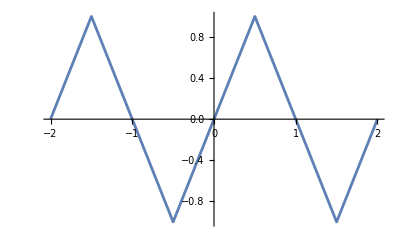

```mathematica
Plot[tr[η,1],{η,-2,2}]
```

```mathematica
u[t_,x_,c_,f_]:=(f[x+c t]+f[x-c t])/2
```

```mathematica
Animate[Plot[u[t,x,1,tr[#,1]&],{x,0,1},PlotRange->{{0,1},{-1,1}}],{t,0,3},AnimationRunning->False]
```

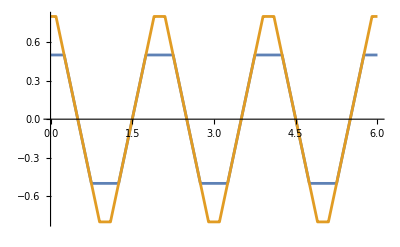

```mathematica
Plot[{u[t,0.25,1,tr[#,1]&],u[t,0.6,1,tr[#,1]&]},{t,0,6}]
```

```mathematica
Simplify[2/L Integrate[Sin[π/L n x]Sin[π/L m x],{x,0,L}]]
```

(2 n Cos[n π] Sin[m π]-2 m Cos[m π] Sin[n π])/(m^2 π-n^2 π)

```mathematica
FullSimplify[4/L^2 A Integrate[x Sin[π/L n x],{x,0,L/2}],Assumptions->n∈Integers&&n>0]
```

-(2 A (n π Cos[(n π)/2]-2 Sin[(n π)/2]))/(n^2 π^2)

```mathematica
FullSimplify[4/L^2 A Integrate[(L-x) Sin[π/L n x],{x,L/2,L}],Assumptions->n∈Integers&&n>0]
```

(2 A (n π Cos[(n π)/2]+2 Sin[(n π)/2]))/(n^2 π^2)

```mathematica
FullSimplify[4/L^2 A Integrate[x Sin[π/L n x],{x,0,L/2}]+4/L^2 A Integrate[(L-x) Sin[π/L n x],{x,L/2,L}],Assumptions->n∈Integers&&n≠0]
```

(8 A Sin[(n π)/2])/(n^2 π^2)

```mathematica
Sum[1/(2n+1)^2,{n,0,∞}]
```

π^2/8

```mathematica
L=Quantity[30,"Centimeters"];
A=Quantity[1,"Centimeters"];
μ=Quantity[0.91,"Grams"/"Meters"];
ω=Quantity[440,"Hertz"];
```

```mathematica
UnitConvert[4 L^2 μ ω^2,"Newtons"]
```

63.4234 N

```mathematica
T=Quantity[63.4,"Newtons"];
```

```mathematica
UnitConvert[Sqrt[T/μ],"Meters"/"Seconds"]
```

263.951 m/s